```mathematica
$Assumptions=Element[{a,b,θ,ϕ,ψ,θ1,ϕ1,ψ1,θ2,ϕ2,ψ2,x1,y1,z1,x2,y2,z2},Reals]&&0<γ<Pi/2&&Element[γ,Reals];
```

```mathematica
ScaledAntiHermitianMatrix[a_]:={{I a,1},{-1,I a}};
(*This prefactor can be removed, it simplified things in some cases*)

JtrigForm[a_,b_,γ_] =(MatrixExp[-I γ/2 KroneckerProduct[ScaledAntiHermitianMatrix[a],ScaledAntiHermitianMatrix[b]]]//TrigToExp)//ExpToTrig//FullSimplify;
J[a_,b_,γ_] =(1/(ⅇ^(1/2 ⅈ a b γ)ⅇ^(-1/2 ⅈ (1+a+b) γ))(MatrixExp[-I γ/2 KroneckerProduct[ScaledAntiHermitianMatrix[a],ScaledAntiHermitianMatrix[b]]]//TrigToExp))//FullSimplify;
```

```mathematica
J[a,b,γ]//MatrixForm
JtrigForm[a,b,g]//MatrixForm
```

(1/4 (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ)) | 1/4 ⅈ (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ)) | 1/4 ⅈ (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ)) | 1/4 (-ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))
1/4 ⅈ (-ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ)) | 1/4 (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ)) | 1/4 (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ)) | 1/4 ⅈ (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))
1/4 ⅈ (-ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ)) | 1/4 (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ)) | 1/4 (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ)) | 1/4 ⅈ (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))
1/4 (-ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ)) | 1/4 ⅈ (-ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ)) | 1/4 ⅈ (-ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ)) | 1/4 (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ)))

(ⅇ^(1/2 ⅈ a b g) (Cos[g/2] Cos[(a g)/2] Cos[(b g)/2]-ⅈ Sin[g/2] Sin[(a g)/2] Sin[(b g)/2]) | ⅇ^(1/2 ⅈ a b g) (Cos[g/2] Cos[(b g)/2] Sin[(a g)/2]+ⅈ Cos[(a g)/2] Sin[g/2] Sin[(b g)/2]) | ⅇ^(1/2 ⅈ a b g) (ⅈ Cos[(b g)/2] Sin[g/2] Sin[(a g)/2]+Cos[g/2] Cos[(a g)/2] Sin[(b g)/2]) | ⅇ^(1/2 ⅈ a b g) (-ⅈ Cos[(a g)/2] Cos[(b g)/2] Sin[g/2]+Cos[g/2] Sin[(a g)/2] Sin[(b g)/2])
-ⅇ^(1/2 ⅈ a b g) (Cos[g/2] Cos[(b g)/2] Sin[(a g)/2]+ⅈ Cos[(a g)/2] Sin[g/2] Sin[(b g)/2]) | ⅇ^(1/2 ⅈ a b g) (Cos[g/2] Cos[(a g)/2] Cos[(b g)/2]-ⅈ Sin[g/2] Sin[(a g)/2] Sin[(b g)/2]) | ⅈ ⅇ^(1/2 ⅈ a b g) (Cos[(a g)/2] Cos[(b g)/2] Sin[g/2]+ⅈ Cos[g/2] Sin[(a g)/2] Sin[(b g)/2]) | ⅇ^(1/2 ⅈ a b g) (ⅈ Cos[(b g)/2] Sin[g/2] Sin[(a g)/2]+Cos[g/2] Cos[(a g)/2] Sin[(b g)/2])
-ⅈ ⅇ^(1/2 ⅈ a b g) (Cos[(b g)/2] Sin[g/2] Sin[(a g)/2]-ⅈ Cos[g/2] Cos[(a g)/2] Sin[(b g)/2]) | ⅈ ⅇ^(1/2 ⅈ a b g) (Cos[(a g)/2] Cos[(b g)/2] Sin[g/2]+ⅈ Cos[g/2] Sin[(a g)/2] Sin[(b g)/2]) | ⅇ^(1/2 ⅈ a b g) (Cos[g/2] Cos[(a g)/2] Cos[(b g)/2]-ⅈ Sin[g/2] Sin[(a g)/2] Sin[(b g)/2]) | ⅇ^(1/2 ⅈ a b g) (Cos[g/2] Cos[(b g)/2] Sin[(a g)/2]+ⅈ Cos[(a g)/2] Sin[g/2] Sin[(b g)/2])
ⅇ^(1/2 ⅈ a b g) (-ⅈ Cos[(a g)/2] Cos[(b g)/2] Sin[g/2]+Cos[g/2] Sin[(a g)/2] Sin[(b g)/2]) | -ⅈ ⅇ^(1/2 ⅈ a b g) (Cos[(b g)/2] Sin[g/2] Sin[(a g)/2]-ⅈ Cos[g/2] Cos[(a g)/2] Sin[(b g)/2]) | -ⅇ^(1/2 ⅈ a b g) (Cos[g/2] Cos[(b g)/2] Sin[(a g)/2]+ⅈ Cos[(a g)/2] Sin[g/2] Sin[(b g)/2]) | ⅇ^(1/2 ⅈ a b g) (Cos[g/2] Cos[(a g)/2] Cos[(b g)/2]-ⅈ Sin[g/2] Sin[(a g)/2] Sin[(b g)/2]))

## Entanglement

```mathematica
EntanglementMeasure[ψ_List]:=Module[{ρFull,ρPartial,eigenvals},(*This assumes ψ is normalized*)
ρFull = Outer[Times,ψ,Conjugate[ψ]]//ComplexExpand//FullSimplify;
ρPartial = ρFull[[{1,2},{1,2}]]+ρFull[[{3,4},{3,4}]];
eigenvals=DeleteCases[Eigenvalues[ρPartial],0];
-Total[Table[λ Log[2,λ],{λ,eigenvals}]]
]
```

```mathematica
EntanglementMeasureNoReduction[ψ_List]:=Module[{ρFull,ρPartial,eigenvals},(*This assumes ψ is normalized*)
ρFull = Outer[Times,ψ,Conjugate[ψ]]//ComplexExpand;
ρPartial = ρFull[[{1,2},{1,2}]]+ρFull[[{3,4},{3,4}]];
eigenvals=DeleteCases[Eigenvalues[ρPartial],0];
-Total[Table[λ Log[2,λ],{λ,eigenvals}]]
]
```

```mathematica
EntangledState = J[a,b,γ].{1,0,0,0}//ExpToTrig//FullSimplify;
EntangledState
```

{1/4 (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ)),1/4 ⅈ (-ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ)),1/4 ⅈ (-ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ)),1/4 (-ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))}

```mathematica
entanglement = EntanglementMeasure[EntangledState]//FullSimplify
```

(Log[4 Csc[γ]^2]+2 Cos[γ] Log[Tan[γ/2]])/Log[4]

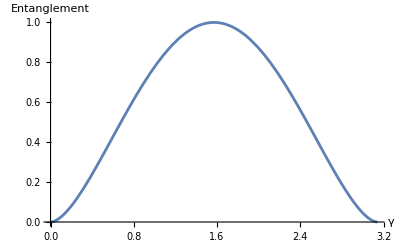

```mathematica
Plot[entanglement,{γ,0,Pi},AxesLabel->{"γ","Entanglement"}]
```

```mathematica
Maximize[entanglement,γ]//FullSimplify
```

{1,{γ→π/2}}

## Strategy Spaces

```mathematica
PauliMatrix[{1,2,3}]
```

{{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{1,0},{0,-1}}}

### Full SU2

```mathematica
su2[θ_,ϕ_,ζ_]:=Module[{n},
(*Define the unit vector using theta and phi*)n={Sin[θ]*Cos[ϕ],Sin[θ]*Sin[ϕ],Cos[θ]};
(*Construct and return the SU(2) matrix*)MatrixExp[-I ζ/2 n.PauliMatrix[{1,2,3}]]//Simplify]
```

```mathematica
so3[θ_,ϕ_,ζ_]:=Module[{nx,ny,nz,K},{nx,ny,nz}={Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
K={{0,-nz,ny},{nz,0,-nx},{-ny,nx,0}};
IdentityMatrix[3]+Sin[ζ] K+(1-Cos[ζ]) K.K]
```

### Rotation Group

```mathematica
MatrixForm/@rotationGroupTrigRepresentation[4]
```

{(1 | 0
0 | 1),(0 | -1
1 | 0),(-1 | 0
0 | -1),(0 | 1
-1 | 0)}

```mathematica
rotationGroupTrigRepresentation[4]
```

{{{1,0},{0,1}},{{0,-1},{1,0}},{{-1,0},{0,-1}},{{0,1},{-1,0}}}

```mathematica
rotationGroupTrigRepresentation[n_]:=Module[{r},
r={{Cos[(2π)/n],-Sin[(2π)/n]},{Sin[(2π)/n],Cos[(2π)/n]}};
Table[MatrixPower[r,k],{k,0,n-1}]]
```

### Dihedral group

```mathematica
dihedralGroupTrigRepresentation[n_]:=Module[{s,rotations,reflections},
s={{0,1},{1,0}};
(*Construct group elements using the new matrices*)rotations=rotationGroupTrigRepresentation[2n];reflections=Table[s.r,{r,rotations}];
Join[rotations,reflections]
]
```

```mathematica
tst = {{0,1},{1,0}};
tst.tst
```

{{1,0},{0,1}}

```mathematica
dihedralGroupTrigRepresentation[4]
```

{{{1,0},{0,1}},{{0,-1},{1,0}},{{-1,0},{0,-1}},{{0,1},{-1,0}},{{0,1},{1,0}},{{1,0},{0,-1}},{{0,-1},{-1,0}},{{-1,0},{0,1}}}

```mathematica
Clear[c]
```

```mathematica
Dic[n_]:=Module[{s,r,rotations,reflections},
s={{I,0},{0,I}};
(*Construct group elements using the new matrices*)rotations=rotationGroupTrigRepresentation[n];reflections=Table[s.r,{r,rotations}];
Join[rotations,reflections]
]
```

```mathematica
Table[d//MatrixForm,{d,dihedralGroupTrigRepresentation[4]}]
```

{(1 | 0
0 | 1),(0 | -1
1 | 0),(-1 | 0
0 | -1),(0 | 1
-1 | 0),(0 | 1
1 | 0),(1 | 0
0 | -1),(0 | -1
-1 | 0),(-1 | 0
0 | 1)}

### Binary Tetrahedral group

```mathematica
binaryTetrahedralGroup:=Module[{qi,qj,qk,q,epsilon,generators,G,newElements,product,nextNew},
(*Define the quaternion representation via 2×2 complex matrices*)
qi={{I,0},{0,-I}};
qj={{0,1},{-1,0}};
qk={{0,I},{I,0}};
q[a_,b_,c_,d_]:=a IdentityMatrix[2]+b qi+c qj+d qk;

(*Define generators:epsilon=(1+i+j+k)/2 and gen2=i (represented by qi)*)epsilon=q[1/2,1/2,1/2,1/2];generators={epsilon,qi};

(*Compute the group closure starting from the identity*)
G={IdentityMatrix[2]};
newElements=generators;

While[newElements!={},nextNew={};
Do[Do[product=Simplify[g1.g2];
If[Not[MemberQ[G,product]],AppendTo[nextNew,product];
AppendTo[G,product];],{g2,generators}],{g1,newElements}];
newElements=nextNew;];

G
]
```

```mathematica
pauliMatrices={IdentityMatrix[2],PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};

pauliGroup=Flatten[Table[s*P,{s,{1,-1,I,-I}},{P,pauliMatrices}],1];
```

```mathematica
Table[m//MatrixForm,{m,pauliGroup}]
```

{(1 | 0
0 | 1),(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1),(-1 | 0
0 | -1),(0 | -1
-1 | 0),(0 | ⅈ
-ⅈ | 0),(-1 | 0
0 | 1),(ⅈ | 0
0 | ⅈ),(0 | ⅈ
ⅈ | 0),(0 | 1
-1 | 0),(ⅈ | 0
0 | -ⅈ),(-ⅈ | 0
0 | -ⅈ),(0 | -ⅈ
-ⅈ | 0),(0 | -1
1 | 0),(-ⅈ | 0
0 | ⅈ)}

```mathematica
su2[1,1,1]//FullSimplify
su2[2,2,2]//FullSimplify
```

{{Cos[1/2]+1/2 ⅈ (Sin[1/2]-Sin[3/2]),-ⅈ ⅇ^-ⅈ Sin[1/2] Sin[1]},{Sin[1/2] Sin[1] (-ⅈ Cos[1]+Sin[1]),Cos[1/2]-1/2 ⅈ (Sin[1/2]-Sin[3/2])}}

{{Cos[1]-ⅈ Cos[2] Sin[1],-ⅈ ⅇ^(-2 ⅈ) Sin[1] Sin[2]},{Sin[1] Sin[2] (-ⅈ Cos[2]+Sin[2]),Cos[1]+ⅈ Cos[2] Sin[1]}}

## Playing The Game

```mathematica
play[j,E^(I ϕ)A,E^(I ψ)B]//MatrixForm
```

{{1/4 (2+2 ⅇ^(-ⅈ Conjugate[γ])),0,0,1/4 (2-2 ⅇ^(-ⅈ Conjugate[γ]))},{0,1/4 (2+2 ⅇ^(-ⅈ Conjugate[γ])),1/4 (-2+2 ⅇ^(-ⅈ Conjugate[γ])),0},{0,1/4 (-2+2 ⅇ^(-ⅈ Conjugate[γ])),1/4 (2+2 ⅇ^(-ⅈ Conjugate[γ])),0},{1/4 (2-2 ⅇ^(-ⅈ Conjugate[γ])),0,0,1/4 (2+2 ⅇ^(-ⅈ Conjugate[γ]))}}.KroneckerProduct[A ⅇ^(ⅈ ϕ),B ⅇ^(ⅈ ψ)].{1/4 (2+2 ⅇ^(ⅈ γ)),0,0,1/4 (2-2 ⅇ^(ⅈ γ))}

```mathematica
Manipulate[J[0,0,g]//N//MatrixForm,{g,0,Pi}]
```

```mathematica
play[J_,d1_,d2_]:=ConjugateTranspose[J].(KroneckerProduct[d1,d2].(J.{1,0,0,0}))//ComplexExpand//Simplify//Chop
alicesScore[ψ_]:=((ψ*Conjugate[ψ]).{3,0,5,1})//Chop;
bobsScore[ψ_]:=((ψ*Conjugate[ψ]).{3,5,0,1})//Chop;
scores[ψ_]:={alicesScore[ψ],bobsScore[ψ]};
```

#### Testing the classical cases

```mathematica
cooperateMove = IdentityMatrix[2];
defectMove = {{0,1},{-1,0}};
classicalMoves = {cooperateMove,defectMove};
```

Classical Payoff matrix for Allice

```mathematica
Table[alicesScore[play[J[0,0,0],m1,m2]],{m1,classicalMoves},{m2,classicalMoves}]//MatrixForm
```

(3 | 0
5 | 1)

Classical Payoff matrix for Bob

```mathematica
Table[bobsScore[play[J[0,0,0],m1,m2]],{m1,classicalMoves},{m2,classicalMoves}]//MatrixForm
```

(3 | 5
0 | 1)

## Identifying Nash Equilibria

```mathematica
numericNashEquilibria[A_,B_]:=Module[{m,n,eqs},
{m,n}=Dimensions[A];
eqs=Select[Flatten[Table[{i,j},{i,m},{j,n}],1],With[{i0=#[[1]],j0=#[[2]]},AllTrue[Range[m],(If[#==i0,True,A[[#,j0]]<=A[[i0,j0]]])&]&&AllTrue[Range[n],(If[#==j0,True,B[[i0,#]]<=B[[i0,j0]]])&]]&];
eqs]
```

```mathematica
symbolicNashEquilibria[A_,B_]:=Module[{m,n,eqs={},cond1,cond2,sol},{m,n}=Dimensions[A];
Table[(*Player 1:no row deviation improves payoff*)cond1=And@@Table[A[[i0,j0]]>=A[[i,j0]],{i,m}];
(*Player 2:no column deviation improves payoff*)cond2=And@@Table[B[[i0,j0]]>=B[[i0,j]],{j,n}];
cond1&&cond2,{i0,m},{j0,n}]]
```